```mathematica
LaserDriftPlot[driftCSV_,trial_,hue_]:= Module[{driftData=driftCSV,run=trial,color=hue},
ListPlot[Drop[Import[driftData,{"Data",All,{1,2}}],{1,3}],PlotLabels->{run}, PlotStyle->color 
,AxesLabel->{"Time(s)","Frequency Change (GHz)"}]]

file=Import["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail2.csv",{"Data",All}];
Take[file,{4}];

	

Trial2=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail2.csv","Lock Trial 2",Red];
```

```mathematica
NoLocking=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv","No Locking",Blue];
```

```mathematica
Trial4=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trial4.csv","Trial 4",Magenta];
```

```mathematica
Trial3=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail3.csv","Trial 3",Green];

Trial3=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail3.csv","Trial 3",Green];
Trial6=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial6.csv","Trial 3",Yellow]

Trial5=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial4.csv","Trial 4",Orange]

Trial7=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv","Trial 7",Blue]
```

-Graphics-

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial4.csv not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,{1,3}].

Drop::drop: Cannot drop positions 1 through 2 in Charting`ChartLabelingDump`getLength[$Failed].

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1,3}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 4},PlotStyle→RGBColor[1, 0.5, 0],AxesLabel→{Time(s),Frequency Change (GHz)}]

-Graphics-

```mathematica
Show[Trial5,Trial6,ImageSize->Large,PlotRange->{{0,100},{-0.010,0.006}}]
```

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 4},PlotStyle→RGBColor[1, 0.5, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],,ImageSize→Large,PlotRange→{{0,100},{-0.01,0.006}}].

Show[ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 4},PlotStyle→RGBColor[1, 0.5, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-,ImageSize→Large,PlotRange→{{0,100},{-0.01,0.006}}]

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListPlot[Drop[$Failed,{1,3}],PlotLabels→{Trial 4},PlotStyle→RGBColor[1, 0.5, 0],AxesLabel→{Time(s),Frequency Change (GHz)}],PlotRange→{{0,100},{-0.01,0.006}},ImageSize→Large,PlotLabel→LaserDrift]

Show::gtype: Show is not a type of graphics.

```mathematica
-Graphics-ListPlot[Drop[$Failed,{1,3}],PlotLabels->{"Trial 4"},PlotStyle->RGBColor[1, 0.5, 0],AxesLabel->{"Time(s)","Frequency Change (GHz)"}],PlotRange->{{0,100},{-0.01,0.006}},ImageSize->Large,PlotLabel->"LaserDrift"],ImageSize->Tiny]
```

```mathematica
Show[%328,ImageSize->Large]
```

-Graphics-

Import Directory of Data

```mathematica
directory="/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/DataAnalysis/mathematicaAnalysis";fileList=Import[directory];
SetDirectory[directory];
```

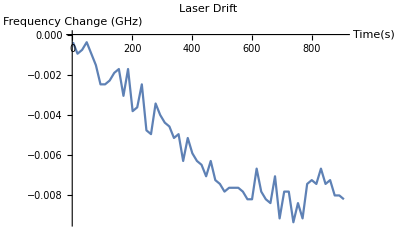
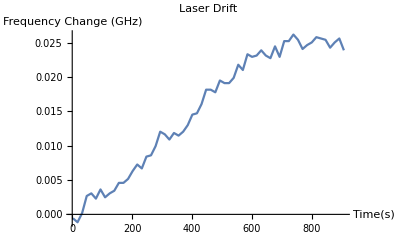
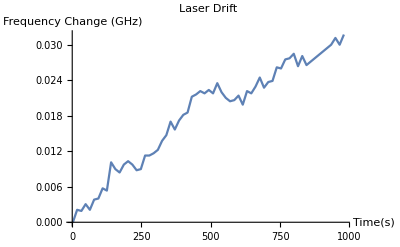

```mathematica
LaserDriftPlotTest[driftCSV_]:= Module[{driftData=driftCSV},
file=Import[driftData,{"Data",All,{1,3}}];

ListLinePlot[Drop[file,{1,3}]
,AxesLabel->Take[file,{4}]]]
Map[LaserDriftPlot,data]
```

```mathematica
filedata=Import["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21trail3.csv",{"Data",Part[9;;],{1,3}}]
```

{{2.41,128.211},{17.721,128.194},{33.067,128.194},{48.398,128.177},{63.728,128.177},{79.054,128.211},{94.377,128.211},{109.703,128.186},{125.036,128.186},{140.364,128.211},{155.692,128.219},{171.023,128.194},{186.346,128.194},{201.673,128.219},{217.007,128.194},{232.327,128.211},{247.66,128.194},{262.995,128.211},{278.323,128.194},{293.651,128.219},{308.978,128.211},{324.305,128.228},{339.635,128.194},{355.002,128.186},{370.318,128.219},{385.654,128.219},{400.982,128.211},{416.311,128.219},{431.646,128.202},{446.976,128.219},{462.294,128.236},{477.638,128.219},{492.966,128.202},{508.297,128.236},{523.613,128.211},{538.941,128.202},{554.28,128.186},{569.626,128.211},{584.955,128.228},{600.269,128.228},{615.612,128.211},{630.924,128.211},{646.282,128.245},{661.642,128.228},{676.967,128.194},{692.295,128.211},{707.647,128.211},{722.973,128.245},{738.306,128.253},{753.625,128.245},{768.952,128.219},{784.282,128.228},{799.608,128.245},{814.942,128.236},{830.274,128.219},{845.595,128.211},{860.919,128.236},{876.253,128.219},{891.578,128.228},{906.908,128.219}}

```mathematica
Trial7=LaserDriftPlot["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-22trial7.csv","Trial 7",Blue]
```

-Graphics-

```mathematica
Show[Trial7, PlotRange->{{0,1500},{-0.020,0.02}},ImageSize->Large,PlotLabel->"LaserDrift"]
```

-Graphics-